```mathematica
EnergyFunc[X_,Y_]:=(
n = Length[X];
m = Length[Y];
A1 = Sum[Abs[X[[i]] - Y[[j]]],{i,1,n},{j,1,m}]/(n m);
A2 = Sum[Abs[X[[i]] - X[[j]]],{i,1,n},{j,1,n}]/(n n);
A3 = Sum[Abs[Y[[i]] - Y[[j]]],{i,1,m},{j,1,m}]/(m m);
Energy = (n m) (2 A1 - A2 - A3) / (n+m);
Return[Energy];
)
```

```mathematica
EnergyData=Table[EnergyFunc[
RandomVariate[NormalDistribution[0,1],100],
RandomVariate[NormalDistribution[0,1],100]
]
,{i,1,500}
];
```

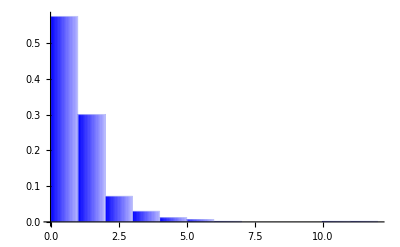

```mathematica
plt1=Histogram[EnergyData,15,"Probability",ChartStyle->Blue,ChartElementFunction->"FadingRectangle"]
```

```mathematica
EnergyData2=Table[EnergyFunc[
RandomVariate[NormalDistribution[-1,1],100],
RandomVariate[NormalDistribution[1,1],100]
]
,{i,1,500}
];
```

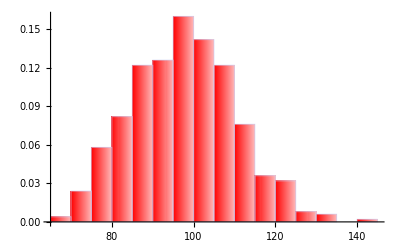

```mathematica
plt2=Histogram[EnergyData2,15,"Probability",ChartStyle->Red,ChartElementFunction->"FadingRectangle"]
```

```mathematica
EnergyData3=Table[EnergyFunc[
RandomVariate[NormalDistribution[0,1],100],
RandomVariate[NormalDistribution[0,1.5],100]
]
,{i,1,500}
];
```

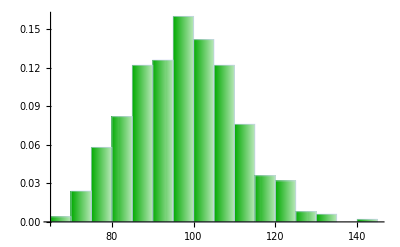

```mathematica
plt3=Histogram[EnergyData2,15,"Probability",ChartStyle->Darker[Green],ChartElementFunction->"FadingRectangle"]
```

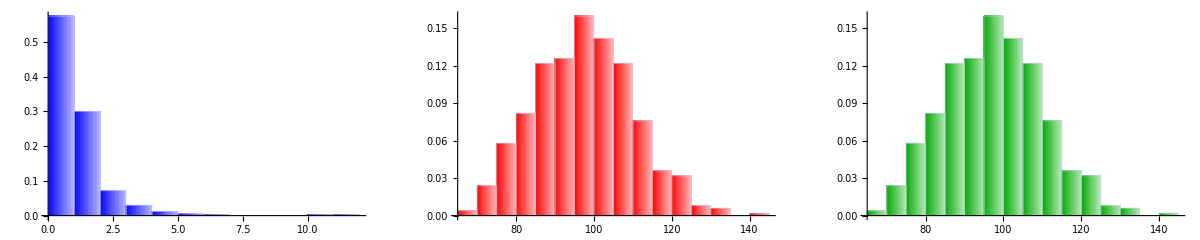

```mathematica
a=GraphicsRow[{plt1,plt2,plt3},ImageSize->Scaled[1]]
```